## Input

```mathematica
img1=-Graphics-;
{face,end,start,app1,app2}={{105,121,64},{112,230,122},{72,212,97},{141,200,106},{255,252,176}};
```

## Image Processing

```mathematica
takecolor[img_,col_]:=Image@Unitize@Map[Total,Unitize[ImageData[img,"Byte"]-Developer`ToPackedArray@ConstantArray[col,Reverse@ImageDimensions@img]],{2}]


trans[img_,mat_]:=ImageTransformation[img,TransformationFunction[mat],DataRange->{{1,1080},{1,1920}},PlotRange->All];
transrd[img_]:=trans[img,({{0.8154, -0.8154, 0.}, {0.5789, 0.5789, 0.}, {0., 0., 1.}})]
transblock[img_]:=trans[img,({{0.8154, 0, 0.}, {-0.5789, 1, 0.}, {0., 0., 1.}})]



rd=ImageMultiply@@(takecolor[transrd@img1,#]&/@{app1,app2});
st=takecolor[transrd@img1,start];
ed=takecolor[transrd@img1,end];
faces=takecolor[transblock@img1,face];



valid=Block[{dat=ComponentMeasurements[DeleteSmallComponents@ColorNegate@DeleteSmallComponents@rd,"BoundingBox"][[;;,2]]},(#1+#2)/2&@@@Pick[dat,Abs[1-Divide@@@Subtract@@@dat],_?(#≤.03&)]];



coordsys=Sort[Mean/@Gather[#,Abs[#1-#2]<10&]]&/@Transpose@valid;
{beginx,beginy}=coordsys[[;;,1]];
{gapx,gapy}=Mean@TakeLargestBy[Gather[#,Abs[#1-#2]<2&],Length,1][[1]]&/@Differences/@coordsys;

findcoor[{x0_,y0_}]:=Block[{rs=Round[({x0,y0}-{beginx,beginy})/{gapx,gapy}],err},If[(err=Max[Abs[rs*{gapx,gapy}+{beginx,beginy}-{x0,y0}]/{gapx,gapy}])>.04,Echo[err]];rs]



{startpoint,endpoint}=findcoor[ComponentMeasurements[DeleteSmallComponents@ColorNegate@#,"Centroid"][[1,2]]]&/@{st,ed};
map=Join[{startpoint,endpoint},findcoor/@valid];
maparr=SparseArray[map+1->1];
frontface=Block[{comp=ComponentMeasurements[ColorNegate@faces,"Image"][[;;,2]]},Map[Round[Mean@Flatten@ImageData[#,"Byte"]/255]&,Reverse@ImagePartition[#,{48,40}]&/@comp,{3}]];
```

## Functions and Calculations

```mathematica
matrixrot::misuse="argument is not valid.";
matrixrot[mat_,dir_]:=Switch[dir,{0.1,0.},Reverse@Transpose@mat,{0.,-0.1},Reverse/@Reverse@mat,{-0.1,0.},Transpose@Reverse@mat,{0.,0.1},mat,_,Message[matrixrot::misuse]];

addposition[prevsize_,currsize_,tardir_]:=Switch[tardir,{1,0,0},{prevsize[[1]],0},{0,1,0},{0,prevsize[[2]]},{-1,0,0},{-currsize[[1]],0},{0,-1,0},{0,-currsize[[2]]}];

faceasso[face_]:=<|1->List/@Reverse@face[[1]],2->List/@face[[;;,-1]],3->face,4->List/@face[[;;,1]],5->Reverse/@face,6->List/@Reverse@face[[-1]]|>



facedir=N@{{0,0.1,-1},{0,-1,0.1},{1,0,0.1},{0,1,0.1},{-1,0,0.1},{0,0.1,1}};
init=startpoint;



nextunfold[facedir_,origin_,face_,history_,prevsize_]:=Block[{faces,allrotdir},
faces=faceasso[face];

If[Length[allrotdir=Select[Round@facedir,#[[1]]+#[[2]]≠0&]]≠0,

Do[Block[{newf,num,downside,neworigin},
newf=(facedir/._?(Round[#]=={0,0,-1}&)->{0.,0.,0.}).RotationMatrix[-Pi/2,{-tardir[[2]],tardir[[1]],0}];
num=Position[newf[[;;,-1]],-1.][[1,1]];
downside=matrixrot[faces[num],newf[[num,;;2]]];
neworigin=origin+addposition[Reverse@Dimensions@prevsize,Reverse@Dimensions@downside,tardir];
If[neworigin[[1]]≥1&&neworigin[[2]]≥1&&neworigin[[1]]+Length@downside[[1]]≤Length@maparr&&neworigin[[2]]+Length@downside≤Length@maparr[[1]]&&
Total@Flatten[maparr[[neworigin[[1]]+1;;neworigin[[1]]+Length@downside[[1]],neworigin[[2]]+1;;neworigin[[2]]+Length@downside]]*Transpose@downside]==Total@Flatten@downside,If[Or@@((neworigin+#==endpoint)&/@(Position[Transpose@faceasso[face][1],1]-1)),Echo[{finalresult=Append[history,tardir],Now-t},"Final Result"];Goto[TheEnd]];nextunfold[newf,neworigin,face,Append[history,tardir],downside]]
]
,{tardir,allrotdir}],

Sow[{history,origin,prevsize}];]
];




oneblock[{history_,inputorigin_},face_]:=Block[{origins=Flatten[Outer[Plus,inputorigin,1-Position[Transpose@faceasso[face[[1]]][1],1],1],1],prevsize=faceasso[face[[1]]][1],temp},Function[{poss,s},Flatten[oneblock[#,s]&/@poss,1]][{#1,Function[{x},#2+x]/@(Position[Transpose@#3,1]-1)}&@@@Flatten[Table[temp=Reap[nextunfold[facedir,origin,face[[1]],Append[history,{face[[1]],origin-Min/@Transpose@inputorigin}],prevsize]];If[Length@temp≠0,temp[[2,1]],Nothing],{origin,origins}],1],Rest@face];]

oneblock[{history_,inputorigin_},{}]:=Block[{},count++;];


res=0;
t=Now;
count=0;
Dynamic[{count,Now-t},UpdateInterval->1,TrackedSymbols:>{}]

Block[{},oneblock[{{},{startpoint}},#]&/@Permutations[frontface];Label[TheEnd];]
```

Part::partw: Part 1 of {} does not exist.

Thread::tdlen: Objects of unequal length in {2}+{0,-1} cannot be combined.

Thread::tdlen: Objects of unequal length in {2}+{0,-1}+{-2} cannot be combined.

Thread::tdlen: Objects of unequal length in {2}+{0,-1}+{0,-3} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Part::span: {3};;{3} is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Final Result {{{{{0,1,0},{1,1,0},{0,1,1},{0,1,0}},{0,-1}},{0,1,0},{1,0,0},{1,0,0},{0,1,0},{1,0,0},{{{1,1,0,0},{0,1,1,0},{0,0,1,1},{0,0,0,1}},{0,-1}},{0,1,0},{1,0,0},{0,1,0},{1,0,0},{0,1,0},{{{1,0},{1,0},{1,1}},{2,1}},{0,1,0},{1,0,0},{1,0,0},{0,1,0},{1,0,0}},0.505012 s}

## Result Interpretation

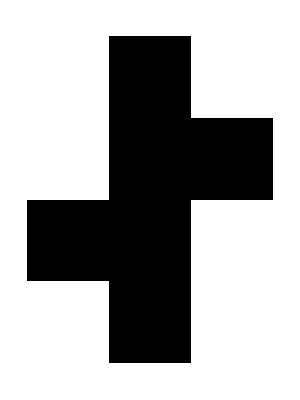
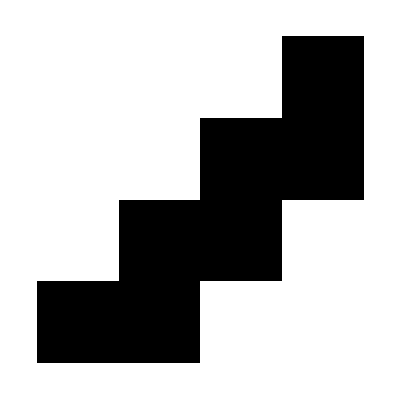
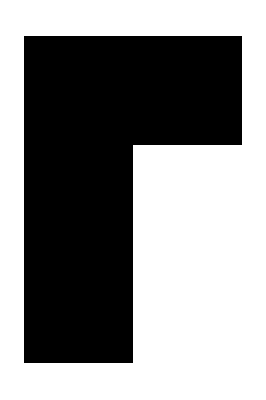
{{-Graphics-,{0,-1},{F,R,R,F,R}},{-Graphics-,{0,-1},{F,R,F,R,F}},{-Graphics-,{2,1},{F,R,R,F,R}}}

```mathematica
interpretdir=<|{1,0,0}->"R",{0,1,0}->"F",{-1,0,0}->"L",{0,-1,0}->"B"|>;
{ArrayPlot[Reverse@#[[1,1]],ImageSize->Tiny],#[[1,2]],interpretdir/@#[[2;;]]}&/@Split[finalresult,Depth[#2]≤Depth[#1]&]
```

## Debug Region

```mathematica
Map[interpretdir,res[[;;,1]],{2}]
```

{{F,R,R,R,F},{F,R,R,F,R},{F,R,F,R,F},{F,R,F,F,R},{F,F,R,F,F}}

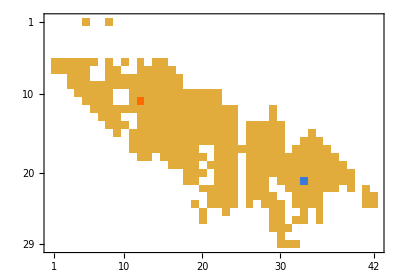

```mathematica
MatrixPlot[ReplacePart[maparr,{startpoint+{1,1}->2,endpoint+{1,1}->-2}]]
```

```mathematica
oneblock[{history_,inputorigin_},face_]:=Block[{origins=Flatten[Outer[Plus,inputorigin,1-Position[Transpose@faceasso[face][1],1],1],1],prevsize=faceasso[face][1]},{{history,{face,#1}},Function[{x},#2+x]/@(Position[Transpose@#3,1]-1)}&@@@Flatten[Table[Reap[nextunfold[facedir,origin,face,{},prevsize]][[2,1]],{origin,origins}],1]]
```